## NDSolve-based discrete Hopf-Cole solution

```mathematica
ν=1/50;
DomainX = {x,0,2π};
L = DomainX[[3]];
DomainT = {t, 0, 1};
u0[x_]:=Cos[x+2Cos[3*x]]+101/100
```

```mathematica
HeatSystem = {
(* Equation *)
D[u[x,t],t] == ν D[u[x,t],{x,2}],
(* Periodic boundary conditions *)
u[0,t]==u[L,t],
(D[u[x,t],x]/.x->0) == (D[u[x,t],x]/.x->L),
(* Initial condition *)
u[x,0]==u0[x]
};
```

```mathematica
HeatSolution =First[NDSolve[HeatSystem,u, DomainX,DomainT]]
```

{u→InterpolatingFunction[{{0.,6.28319},{0.,1.}},<>]}

```mathematica
Plot3D[Evaluate[u[x,t]/.HeatSolution],Evaluate[DomainX],Evaluate[DomainT],PlotRange->All]
```

-Graphics3D-

```mathematica
w[x_,t_]:=(-2 ν D[u[x,t],x]/u[x,t]/.HeatSolution)
```

```mathematica
Plot3D[Evaluate[w[x,t]],Evaluate[DomainX],Evaluate[DomainT],PlotRange->All]
```

-Graphics3D-

```mathematica
w0[x_]:=-2ν D[u0[x],x]/u0[x]
```

```mathematica
w0[x]//FullSimplify
```

(4 (1-6 Sin[3 x]) Sin[x+2 Cos[3 x]])/(101+100 Cos[x+2 Cos[3 x]])

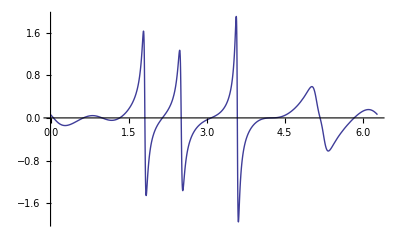

```mathematica
Plot[Evaluate[w0[x]],Evaluate[DomainX],PlotRange->Full]
```